```mathematica
Plot3D[PDF[MultinormalDistribution[{1,1},{{1,0},{0,1}}],{x,y}],{x,-2,4},{y,-2,4},ViewPoint->{-1*Pi/2,-Pi,3*Pi/4}]
```

-Graphics3D-

```mathematica
Plot3D[PDF[MultinormalDistribution[{1,1},{{1,.6},{.6,1}}],{x,y}],{x,-2,4},{y,-2,4},PlotRange->All,ViewPoint->{-1*Pi/2,-Pi,3*Pi/4}]
```

-Graphics3D-

```mathematica
c=.007957;
Integrate[
PDF[MultinormalDistribution[{1,1},{{1,0},{0,1}}],{x,y}]*
If[PDF[MultinormalDistribution[{1,1},{{1,0},{0,1}}],{x,y}]≥c,1,0],
{x,-∞,∞},{y,-∞,∞}]
```

0.950005

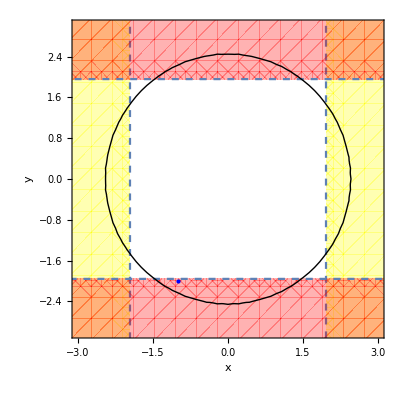

```mathematica
cplotInd=ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}],{x,-3,3},{y,-3,3},Contours->{{.007957,Thick}},ContourShading->None,FrameLabel->{"x","y"}];

Show[
RegionPlot[x≥1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Yellow},PlotRange->{{-3,3},{-3,3}},FrameLabel->{"x","y"}],
RegionPlot[x≤-1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Yellow}],
RegionPlot[y≥1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Red}],
RegionPlot[y<=-1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Red}],
Graphics[{PointSize[Large],Blue,Point[{-1,-2}]}],
cplotInd
]
```

```mathematica
FindRoot[
.95-Integrate[
PDF[MultinormalDistribution[{1,1},{{1,.6},{.6,1}}],{x,y}]*
If[PDF[MultinormalDistribution[{1,1},{{1,.6},{.6,1}}],{x,y}]≥c,1,0],
{x,-∞,∞},{y,-∞,∞}],{c,.07}]
```

{0.007957→0.00994718}

```mathematica
Integrate[
PDF[MultinormalDistribution[{1,1},{{1,.6},{.6,1}}],{x,y}]*
If[PDF[MultinormalDistribution[{1,1},{{1,.6},{.6,1}}],{x,y}]≥.00994718,1,0],
{x,-∞,∞},{y,-∞,∞}]
```

0.95

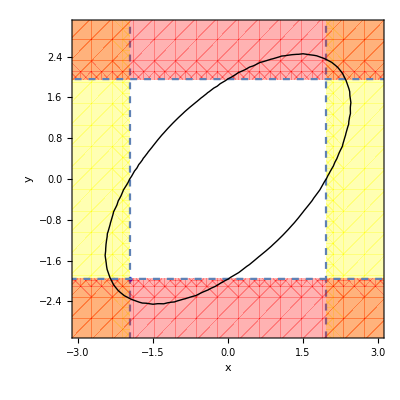

```mathematica
cplotCorr=ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,.6},{.6,1}}],{x,y}],{x,-3,3},{y,-3,3},Contours->{{.00994718,Thick}},ContourShading->None,FrameLabel->{"x","y"}];

Show[
RegionPlot[x≥1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Yellow},PlotRange->{{-3,3},{-3,3}},FrameLabel->{"x","y"}],
RegionPlot[x≤-1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Yellow}],
RegionPlot[y≥1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Red}],
RegionPlot[y<=-1.96,{x,-4,4},{y,-4,4},BoundaryStyle->Dashed,PlotStyle->{Opacity[.3],Red}],
Graphics[{PointSize[Large],Blue,Point[{-1.96,-1.96}]},PlotRange->{-3,3},{-3,3}],
cplotCorr
]
```